(2.36468×10^6 g)/(3.00148×10^6+1.32226×10^19 g^3)

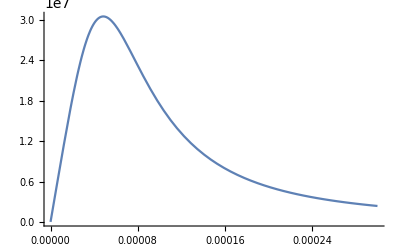

```mathematica
(* Resistance relaxation via diffusive model (Fokker-Planck) *)
ClearAll["Global`*"]
Ea=Quantity[2.25, "Electronvolts"]; (* activation energy *)
c=1.2*10^12; (* fitting param *)
gfiteqn[g_]=(2.3646797834955216*^6 g)/(3.001475758376027*^6+1.3222604723603818*^19 g^3) (* fitting equation *)
σ[g_,T_]:=c gfiteqn[g] (* spread equation *)
Plot[σ[g,Quantity[298, "Kelvins"]], {g,0,0.0003},PlotRange->All]
```

```mathematica
(* Load data on distributions *)
icfnns=Table[ReadList[ToString@StringForm["data/g_2bpc-expt5-pre_range``.csv",i]],{i,0,3}];
icfns=Table[PDF[SmoothKernelDistribution[icfnn],g],{icfnn,icfnns}];
fcfnns=Table[ReadList[ToString@StringForm["data/g_2bpc-expt5-post_range``.csv",i]],{i,0,3}];
fcfns=Table[PDF[SmoothKernelDistribution[fcfnn],g],{fcfnn,fcfnns}];
fns=Table[{icfns[[i]],fcfns[[i]]},{i,4}];
reads={{g,0.0003,0.000196078431},{g,0.000185873606,0.000154320988},{g,0.00014300144,0.0000714285714},{g,0.00006,-0.00001}};
```

```mathematica
(* Parameters *)
T=Quantity[(273+65), "Kelvins"];
maxbound=0.0003; (* units: Siemens *)
time=10*10^9; (* units: seconds *)
```

```mathematica
(* Method *)
method={"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.00000005},"IntegrationOrder"->5}}};
```

```mathematica
(* Equations *)
heqn=D[p[g,t],t]== Exp[-Ea/(Quantity[, "BoltzmannConstant"]T)]D[σ[g,T]^2 p[g,t]/2,{g,2}];
ics=Table[p[g,0]==icfn,{icfn,icfns}];
bc1=DirichletCondition[p[g,t]==0,g≤0];
bc2=DirichletCondition[p[g,t]==0,g≥maxbound];
```

```mathematica
(* Solve *)
sol=Table[NDSolve[{heqn,ic,bc1,bc2},p[g,time],{g,-0.00001,maxbound},{t,0,time},Method->method],{ic,ics}];
dists=Table[p[g,time]/.sol[[i]],{i,4}];
```

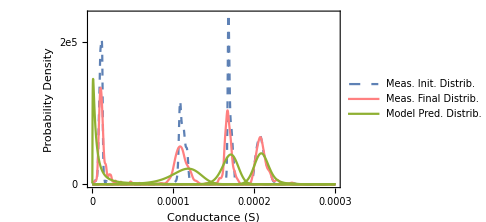

```mathematica
(* Plot *)
data={icfns,fcfns,dists};
plt=Plot[data,{g,0,maxbound},Frame->{{True,False},{True,False}},Axes->None,PlotRange->All,ImageSize->Medium,FrameLabel->{{"Probability Density",None},{"Conductance (S)",None}},FrameTicks->{{Prepend[Table[{i*10^5,ToString[i]<>"e5"},{i,1,5}],{0,0}],All},{All,All}},PlotStyle->{Dashed,Pink,Thick},PlotLegends->{Style["Meas. Init. Distrib.",Black,Bold,11],Style["Meas. Final Distrib.",Black,Bold,11],Style["Model Pred. Distrib.",Black,Bold,11]},LabelStyle->{FontSize->14,FontFamily->"Times",Black,Bold}]
```

```mathematica
(* BER *)
ber=Mean[Table[1+NIntegrate[dists[[i]],reads[[i]]],{i,4}]][[1]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in g near {g} = {-1.84433×10^-8}. NIntegrate obtained -0.954969 and 0.000149786 for the integral and error estimates.

0.122853

```mathematica
(* Export plot *)
Export["retention2bpc.pdf",plt]
Export["retention2bpc.eps",plt]
```

retention2bpc.pdf

retention2bpc.eps

```mathematica
(* Goodness of fit *)
(*err=Total[Table[NIntegrate[(dists[[i]]-fcfns[[i]])^2,{g,0,0.0003}],{i,4}]]*)
```

```mathematica
(* Actual BER *)
actualber=Mean[Table[1+NIntegrate[fcfns[[i]],reads[[i]]],{i,4}]]
```

0.00501487